```mathematica
n=24
```

24

```mathematica
Clear[g]
diff=Table[D[z[i][t],t]==I/(2Pi)Sum[g[j](z[i][t]-z[j][t])/Abs[z[i][t]-z[j][t]]^2,{j,Drop[Range[n],{i}]}],{i,1,n}];
```

```mathematica
(g[#]=2*Random[]-1)&/@Range[n]
```

{0.149312,-0.864921,0.496949,0.365652,0.985987,0.0024709}

```mathematica
Table[Mod[i,4],{i,1,n}]
(g[#]=%[[#]])&/@Range[n]
```

{1,2,3,0,1,2,3,0,1,2,3,0,1,2,3,0,1,2,3,0,1,2,3,0}

{1,2,3,0,1,2,3,0,1,2,3,0,1,2,3,0,1,2,3,0,1,2,3,0}

```mathematica
sol=NDSolve[Evaluate[diff]~Join~((z[#][0]==Exp[2Pi I #/n])&/@Range[n]),z/@Range[n],{t,0,100}];
```

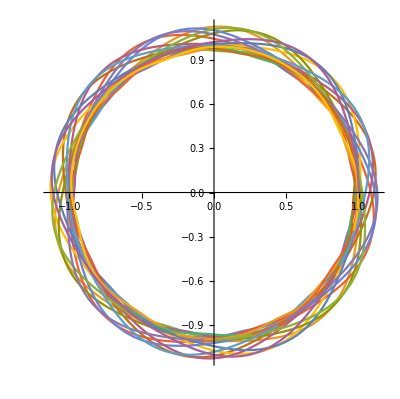

```mathematica
ParametricPlot[Evaluate[{Re[(z[#]/.sol[[1,#]])[t]],Im[(z[#]/.sol[[1,#]])[t]]}&/@Range[n]],{t,0,10}]
```

```mathematica
Manipulate[ListPlot[Evaluate[Style[{Re[(z[#]/.sol[[1,#]])[t]],Im[(z[#]/.sol[[1,#]])[t]]},Hue[(#+0)/n]]&/@Range[n]],PlotRange->{{-2,2},{-2,2}},AspectRatio->Automatic,ImageSize->Large],{t,4.95,5}]
```

```mathematica
Animate[ListPlot[Evaluate[Style[{Re[(z[#]/.sol[[1,#]])[t]],Im[(z[#]/.sol[[1,#]])[t]]},Hue[#/n]]&/@Range[n]],PlotRange->{{-2,2},{-2,2}},AspectRatio->Automatic,ImageSize->Large,Axes->False],{t,0,5},AnimationRunning->False,AnimationRate->.5]
```

```mathematica
SetDirectory[NotebookDirectory[]]
```

/home/adam/Dropbox/personal/projects/mathca

```mathematica
?Export
```

Export[file.ext,expr] exports data to a file, converting it to the format corresponding to the file extension ext. 
Export[file,expr,format] exports data in the specified format.
Export[file,exprs,elems] exports data by treating exprs as elements specified by elems.

```mathematica
Export["vortices-sixfold02.gif",Table[ListPlot[Evaluate[Style[{Re[(z[#]/.sol[[1,#]])[t]],Im[(z[#]/.sol[[1,#]])[t]]},Hue[#/n]]&/@Range[n]],PlotRange->{{-2,2},{-2,2}},AspectRatio->Automatic,ImageSize->Large,Axes->False],{t,0,4.975,.025}]]
```

vortices-sixfold02.gif

```mathematica
Drop[Range[10],{7}]
```

{1,2,3,4,5,6,8,9,10}

```mathematica
Hue[(#+.5)/4]&/@Range[4]
```

{Hue[0.375],Hue[0.625],Hue[0.875],Hue[1.125]}